```mathematica
(* To clear the notebook: NotebookDelete[Cells[]] *)
```

```mathematica
(* To remove variable definitions: ClearAll["Global`*"] *)
```

```mathematica
(* For special characters: esc before and after ie esc pi esc *)

(* To get the value of an expession: N[Sqrt[2]] *)
Sqrt[2]
```

```mathematica
N[Sqrt[2]]
```

√2

1.41421

```mathematica
(* Set and unset value to x: *)
```

```mathematica
x=2
```

2

```mathematica
Unset[x]
```

```mathematica
x=2
```

2

```mathematica
x=.
```

```mathematica
(* Substitution *)
```

```mathematica
x/.x->2
```

2

```mathematica
x+y/.{x->1,y->2}
```

3

```mathematica
(* Delayed assigment *) 
x:=a+1
```

```mathematica
a=1;
```

```mathematica
x
```

2

```mathematica
a=2;
```

```mathematica
x
```

3

```mathematica
(* Random integer *)
x=.
x=RandomInteger[10]
```

0

```mathematica
x=.
x:=RandomInteger[10]
```

```mathematica
x
```

1

```mathematica
x
```

4

```mathematica
(* Expansion *)
x=.
Expand[(x+y)^2]
```

x^2+2 x y+y^2

```mathematica
Sin[(x+y)^2]
ExpandAll[Sin[(x+y)^2]]
```

Sin[(x+y)^2]

Sin[x^2+2 x y+y^2]

```mathematica
(* Substitution for an expression 
p_ is pattern *)
Sin[(x+y)^2]/.Sin[p_]:>Sin[Expand[p]]
```

Sin[x^2+2 x y+y^2]

```mathematica
(* List *)
list={1,a,Cos[k/2]}
```

{1,2,Cos[k/2]}

```mathematica
(* Table(var,start,stop,step) *)
list2=Table[1+i,{i,1,5,0.5}]
```

{2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.}

```mathematica
(* Matrix is a list of list *)
A ={{a11,a12,a13},{a21,a22,a23}}
```

{{a11,a12,a13},{a21,a22,a23}}

```mathematica
MatrixForm[A]
```

(a11 | a12 | a13
a21 | a22 | a23)

```mathematica
B={{b11,b12},{b21,b22}}
```

{{b11,b12},{b21,b22}}

```mathematica
B//MatrixForm
```

(b11 | b12
b21 | b22)

```mathematica
(* Matrix multiplication with . *)
B.A
```

{{a11 b11+a21 b12,a12 b11+a22 b12,a13 b11+a23 b12},{a11 b21+a21 b22,a12 b21+a22 b22,a13 b21+a23 b22}}

```mathematica
Transpose[A]
```

{{a11,a21},{a12,a22},{a13,a23}}

```mathematica
(* Retrieve elements *)
A[[1]]
```

{a11,a12,a13}

```mathematica
A[[1,2]]
```

a12

```mathematica
A[[1,2;;3]]
```

{a12,a13}

```mathematica
C1={{1,2},{1,3}};
Inverse[C1]
Det[C1]
Tr[C1]
Eigenvalues[C1]
N[Eigenvalues[C1]]
Exp[C1]//MatrixForm
MatrixExp[C1]//MatrixForm
```

{{3,-2},{-1,1}}

1

4

{2+√3,2-√3}

{3.73205,0.267949}

(ⅇ | ⅇ^2
ⅇ | ⅇ^3)

(ⅇ^(2-√3)/2+ⅇ^(2-√3)/(2 √3)+ⅇ^(2+√3)/2-ⅇ^(2+√3)/(2 √3) | -ⅇ^(2-√3)/(√3)+ⅇ^(2+√3)/(√3)
-ⅇ^(2-√3)/(2 √3)+ⅇ^(2+√3)/(2 √3) | ⅇ^(2-√3)/2-ⅇ^(2-√3)/(2 √3)+ⅇ^(2+√3)/2+ⅇ^(2+√3)/(2 √3))

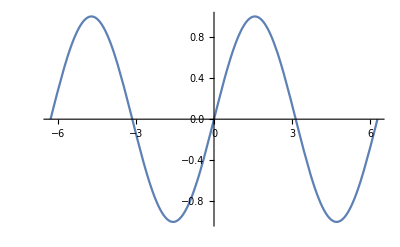

```mathematica
(* Visualization *)
Plot[Sin[x],{x,-2π,2π}]
```

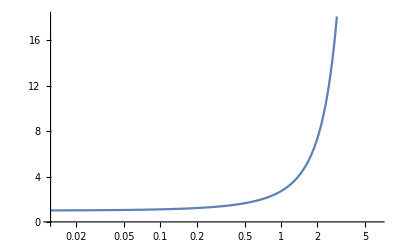

```mathematica
LogLinearPlot[Exp[y],{y,-2π,2π}]
```

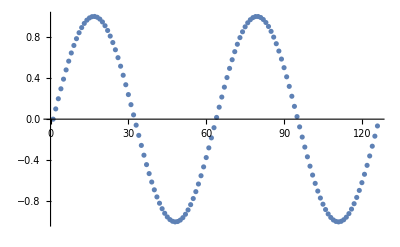

```mathematica
ListPlot[Table[Sin[i],{i,-2π,2π,0.1}]]
```



```mathematica
ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2π}]
```

```mathematica
Plot3D[Exp[-x^2-y^2],{x,-5,5},{y,-5,5},PlotRange->Full]
```

-Graphics3D-

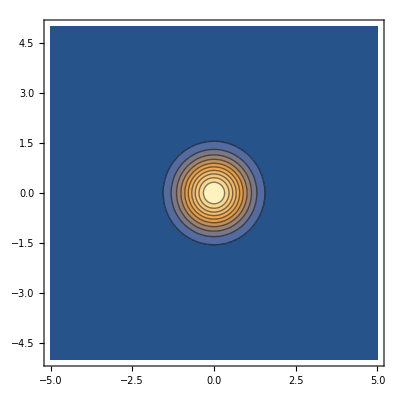

```mathematica
ContourPlot[Exp[-x^2-y^2],{x,-5,5},{y,-5,5},Contours->10,PlotRange->Full]
```

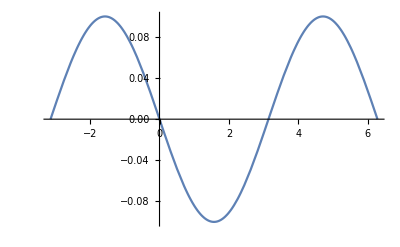

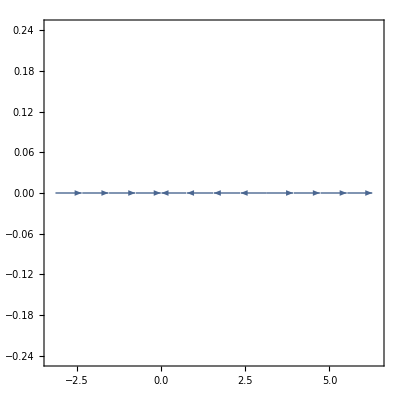

```mathematica
s1=Plot[-0.1Sin[x],{x,-π,2π}]
s2=StreamPlot[{-Sin[x],0},{x,-π,2π},{y,-0.1,0.1},StreamScale->{Automatic,Automatic,0.05}]
```

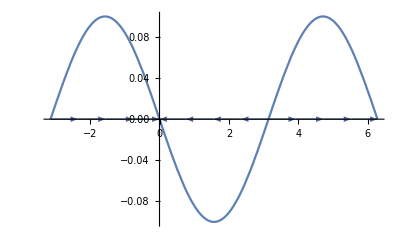

```mathematica
Show[s1,s2]
```

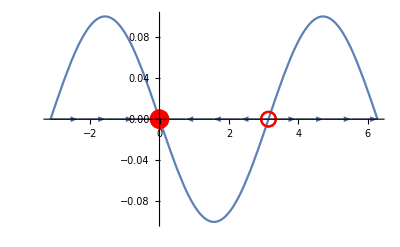

```mathematica
s3 = ListPlot[{{0,0}},PlotMarkers->{Automatic,20},PlotStyle->Red];
s4 = ListPlot[{{π,0}},PlotMarkers->Graphics[{Red,Thick,Circle[]},ImageSize->15]];
Show[s1,s2,s3,s4]
```

```mathematica
(* Differentation *)
D[Log[x],x]
D[f[x],x]
D[f[x],{x,2}]
```

1/x

f'[x]

f''[x]

```mathematica
(* Series Expansion *)
Series[x,{x,0,4}]
Series[Exp[x],{x,0,4}]
```

x+O[x]^5

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

```mathematica
(* Series uses the "Big-O" syntax thats why there is a O[x]^5, we can rid of it with "Normal" *)
s1=.
s1=Series[Exp[x],{x,0,4}];
Normal[s1]
```

1+x+x^2/2+x^3/6+x^4/24

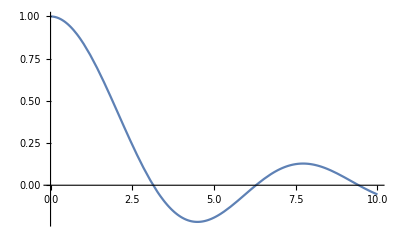

1

```mathematica
(* Limit *)
Plot[Sin[x]/x,{x,0,10}]
Limit[Sin[x]/x,x->0,Direction->1]
```

```mathematica
(* Equation Solving *)
sol=Solve[x^2+x+5==0,x]
```

{{x→1/2 (-1-ⅈ √19)},{x→1/2 (-1+ⅈ √19)}}

```mathematica
sol//Flatten
sol[[1]]
```

{x→1/2 (-1-ⅈ √19),x→1/2 (-1+ⅈ √19)}

{x→1/2 (-1-ⅈ √19)}

```mathematica
{x->-1}
x^2+x+5/.sol[[1]]
```

{x→-1}

5+1/2 (-1-ⅈ √19)+1/4 (-1-ⅈ √19)^2

```mathematica
x^2+x+5/.sol[[1]]//FullSimplify
```

0

```mathematica
(* For differential equations *)
DSolve[y'[x]+y[x]==a Sin[x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])}}

```mathematica
sol2=DSolve[{y'[x]+a*y[x]==0,y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(-a x)}}

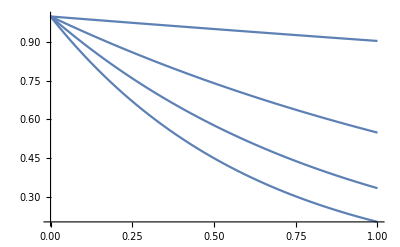

```mathematica
Plot[Table[y[x]/.sol2,{a,0.1,2,0.5}],{x,0,1}]
```

```mathematica
(* Numerical integration of dynamical systems *)
minx=-2;
maxx=2;
miny=-2;
maxy=2;
(* We also add initial conditions *)
solution[x0_,y0_]:=NDSolve[{-x[t]+y[t]+y[t]^2-x[t]^2,-x[t]-y[t]-x[t]*y[t]-y[t]^3,x[0]=x0,y[0]=y0},{x,y},{t,0,10}];
initialConditions = Join[Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.solution[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialConditions]}]]
```

NDSolve::deqn: Equation or list of equations expected instead of -x[t]-x[t]^2+y[t]+y[t]^2 in the first argument {-x[t]-x[t]^2+y[t]+y[t]^2,-x[t]-y[t]-x[t] y[t]-y[t]^3,-2,-2.}.

ReplaceAll::reps: {NDSolve[{-x[t]-x[t]^2+y[t]+y[t]^2,-x[t]-y[t]-x[t] y[t]-y[t]^3,-2,-2.},{x,y},{t,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{-x[0.000204082]-x[0.000204082]^2+y[0.000204082]+y[0.000204082]^2,-x[0.000204082]-y[0.000204082]-x[0.000204082] y[0.000204082]-y[0.000204082]^3,-2,-2.},{x,y},{0.000204082,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{-1. x[0.000204082]-1. x[0.000204082]^2+y[0.000204082]+y[0.000204082]^2,-1. x[0.000204082]-1. y[0.000204082]-1. x[0.000204082] y[0.000204082]-1. y[0.000204082]^3,-2.,-2.},{x,y},{0.000204082,0.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of -x[t]-x[t]^2+y[t]+y[t]^2 in the first argument {-x[t]-x[t]^2+y[t]+y[t]^2,-x[t]-y[t]-x[t] y[t]-y[t]^3,-2,-1.9}.

NDSolve::deqn: Equation or list of equations expected instead of -x[t]-x[t]^2+y[t]+y[t]^2 in the first argument {-x[t]-x[t]^2+y[t]+y[t]^2,-x[t]-y[t]-x[t] y[t]-y[t]^3,-2,-1.8}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

-Graphics-

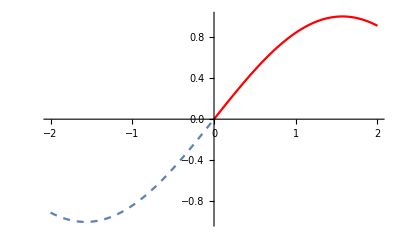

```mathematica
s1=.
s2=.
s1=Plot[Sin[x],{x,-2,0},PlotStyle->Dashed];
s2=Plot[Sin[x],{x,0,2},PlotStyle->Red];
Show[s1,s2,PlotRange->Full]
```

```mathematica
(*Overdamped, driven oscillator *)
(* dx[t]/dt=μ-Sin[x]:constant forcing (torque) is μ , and rescaled so that the frequency is normalised, overdamped which means that we ignore the x''[t]. This equation has qualitatively two differen solutions. If μ<1, then there's a stable fixed point, and if μ>1 then there's no fixed points*)
(* Thus we expect some sort of bifurcation at m=1 *)
f[x_,μ_]:=μ-Sin[x]
Solve[f[x,μ]==0,x]
(* Now caclulate the normal form, series around the solution point *)
Series[f[x,μ],{x,π/2,2},{μ,1,2}]//Normal
(* The normal form for a saddle point birfucation r+1/2(h)^2 where h=(x-π/2) *)
```

{{x→ConditionalExpression[π-ArcSin[μ]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[ArcSin[μ]+2 π C[1],C[1]∈ℤ]}}

-1+1/2 (-π/2+x)^2+μ